```mathematica
(*SetDirectory["C:\\Users\\jwg3\\Desktop\\H"] *)
```

```mathematica
SetDirectory["/home/ltz1/github/ludmil02/Working_dirs/MathBio/nb_Data"]
```

/home/ltz1/github/ludmil02/Working_dirs/MathBio/nb_Data

#### Meta-population reproduction numbers:

```mathematica
m=4; n=4; 
x=1;k=1/5x; ξ=1/2 x; 
γa=1/7;γs=1/5;γm=1/5;γh=1/10 ; 
ω=x 1/(1×182.5);ωv=x 1/(1×182.5)
bS=0.31;bI=0.31;
ϵ1=0.8
ϵ2=0.8 
ϵ3=0.8
vγa=Table[γa,{j,n}]x;
vγs=Table[γs,{j,n}]x; 
vγm=Table[γm,{j,n}]x; 
vγh=Table[γh,{j,n}]x; 
vβ={0.0794498883424254,0.07378658226273424,0.08093055958811815,0.21470494228237624};
vp={0.9706574350846233,0.8938517556772458,0.6548278086229462,0.28889590656079006};
vq={0.9853287175423117,0.9469258778386229,0.8274139043114731,0.6444479532803951};
vδs={0.0005227159753841133,0.010632200553688746,0.02953817543239884,0.057703228431405976};
vδm={0.00026135798769205665,0.005316100276844373,0.01476908771619942,0.028851614215702988};
mN={{12861646,14862307,14294150,13831766},{17039947,18046593,16847952,16382252},{31775045,34108261,31760738,29018710},{19577717,22475544,19374280,17227215}};
ma={{17.073281356320802,17.011021886542494,14.464215476578978,3.6569593567943652},{13.676777723325813,13.626903952047815,11.586751010942738,2.929455634349783},{15.06551341188455,15.010575473629661,12.763266047514328,3.2269116338380703},{13.603540223639197,13.553933520407654,11.524705352915733,2.913768751778259}};
```

0.00547945

0.8

0.8

0.8

```mathematica
mc={{{{0.20197824889699842,0.059415283664697484,0.04892172067444938,0.008030707230540838},{0.1521469690453322,0.044793777860070695,0.03339288184769395,0.002877214165782988},{0.16553227488415234,0.04874272018491846,0.03561633471701904,0.0026950721853331765},{0.13265108985915125,0.03912354820446772,0.023571691514938764,0.0005104650644532836}},{{0.06103198838432115,0.1621666401078013,0.08879328829009539,0.012414165389758761},{0.0459744160482341,0.12225905533493119,0.06060832987601685,0.004447704478623026},{0.050019068553821766,0.13303720313296225,0.06464391343488654,0.004166142642932759},{0.04008332491079227,0.10678286747259674,0.04278279609376618,0.0007890958484599316}},{{0.061021070464599016,0.1080249810376071,0.14362458579558354,0.02178381591253095},{0.04596619175476153,0.08144111591294141,0.09803495784237114,0.00780463064199165},{0.05001012071860447,0.08862082445675072,0.10456257978596326,0.007310558668234078},{0.04007615446566739,0.07113187537338422,0.06920186746625413,0.0013846697027553945}},{{0.0530544005552305,0.07868141298325652,0.11156873991077054,0.14315896066513709},{0.039965027338719886,0.05931870585316376,0.0761543481785637,0.05129050004687597},{0.043480996911706815,0.0645481408191205,0.0812250577010754,0.048043556052264826},{0.03484397005077645,0.05180983517672048,0.05375657036651684,0.009099777390100771}}},{{{0.1864572151389774,0.05489509996649521,0.04092321913380201,0.003526046848494684},{0.15883787710504257,0.04672482099647865,0.038472569688521994,0.006315434929836045},{0.16645777750802396,0.048999330689790524,0.037222141625251635,0.0036235420810433495},{0.1384701016999805,0.04080592480578916,0.02714997342339332,0.0011189243590791157}},{{0.05620517348314829,0.14946555074840534,0.074095594637493,0.005437458989376001},{0.04787967272668808,0.12721993598921966,0.06965844790907054,0.00973892858108688},{0.05017659550199961,0.13341285383071985,0.06739442242768076,0.0055878047877789255},{0.0417400639737951,0.11110427030131684,0.049157751217494744,0.001725474894726343}},{{0.05598955512300673,0.09920012240767083,0.11941240869771409,0.009506504255907459},{0.04769599325596215,0.08443573224488508,0.11226150612140896,0.01702691757031642},{0.049984104409647206,0.08854596503673143,0.10861280423287652,0.009769359198844548},{0.04157993771515215,0.07373978257008608,0.07922259761545583,0.0030167095443343977}},{{0.0483897647994067,0.07182325186748455,0.09220789380625656,0.06210267824107499},{0.041221936671215216,0.0611334816575884,0.08668610865372699,0.11123091673257021},{0.04319946909344056,0.06410938811695327,0.08386865341655675,0.06381981794941248},{0.035936049178990924,0.053389359283444786,0.06117411873395686,0.019707111797920892}}},{{{0.18556130844105437,0.05464047987511577,0.03992583124100672,0.0030211698679518018},{0.1522624964435324,0.04482073788669957,0.034047890652404864,0.003314531597667506},{0.1762963105157434,0.05186051149336481,0.04270122602847936,0.007009586741681536},{0.1370960269820946,0.04041057478883919,0.02613515273683758,0.0008961647075264086}},{{0.05599820943381795,0.14894010182362313,0.07237126775468089,0.004664151792412439},{0.04594938048450658,0.12217325469894243,0.06171666147695607,0.005117050403640263},{0.053202242437334624,0.1413624089704349,0.07740206694021748,0.010821561843342861},{0.041372482744302365,0.11015194481375509,0.04737369461664491,0.001383519765388032}},{{0.055880628953818706,0.09902370436004378,0.11683680502094429,0.008168718861595085},{0.045852899717216664,0.0812276083196121,0.09963591584396908,0.008961918052484497},{0.05309053270114724,0.09398563061336453,0.12495857104461666,0.018952705717133245},{0.04128561217417128,0.07323516960420862,0.07648050521663968,0.002423073799034595}},{{0.04852266901536028,0.07203257273247518,0.09064319750041606,0.05361426218857699},{0.03981531915490311,0.05908720181678404,0.07729857039792182,0.058820315929519154},{0.046099952601390444,0.06836773898448949,0.09694414728763369,0.12439347598050467},{0.03584941923755752,0.053273281535798744,0.05933436418464847,0.01590351145202035}}},{{{0.17692165561991846,0.05218052056270084,0.03143843516862934,0.0006808261012789027},{0.15069897386425823,0.044409666204609816,0.029547700804121193,0.001217741235651662},{0.163113647303639,0.04807955699770153,0.031094993630267853,0.0010662358147586787},{0.1710191212768521,0.05030813792198626,0.04142302315613488,0.0067997643374913255}},{{0.05402593029206072,0.1439262777551564,0.057664386988987765,0.0010635753744862712},{0.046018404183184,0.12249241449207234,0.05419640146414941,0.0019023353956358151},{0.049809428405089215,0.1326148455433863,0.057034446418792614,0.001665656110778397},{0.05222349458769408,0.13876180141215785,0.07597812119836828,0.010622480378000503}},{{0.054942625759409065,0.0975186382104811,0.0948726831888986,0.0018983205922129109},{0.04679923039573194,0.08299591734527946,0.08916695892507336,0.0033953799057967727},{0.050654579557569544,0.08985446817352293,0.09383626963688473,0.002972943310353709},{0.05310960687708606,0.09401939743322546,0.12500346571129078,0.018959514977183435}},{{0.05103757114600094,0.07588825685021303,0.07873972973366654,0.01332886394068318},{0.04347296871757569,0.06458678677837276,0.07400425508103237,0.02384031284122476},{0.04705429841233032,0.06992405846740708,0.07787955670772401,0.020874217479185664},{0.0493348343305421,0.07316517449633562,0.10374681915848274,0.13312229585922322}}}};
```

```mathematica
(* At t0=348 for vψS[t], vS[t], and ψI. *)
(*vψS={0.7781979107138681,0.7798533321459905,0.7865615336962511,0.7801996496586996};*)
vψS={1,1,1,1};
(*vS={0.3584240358428625,0.4311839255813418,0.46185034172622086,0.39168924912805897};*)
vS={1,1,1,1};
(*vψI=ψI={0.7781979107138681,0.7798533321459905,0.7865615336962511,0.7801996496586996};*)
```

```mathematica
vψI=ψI={1,1,1,1};
```

```mathematica
mχ1={{0.840852151925834,0.3997145320288302,0.228651131766539,0.817373846824904},{0.8078053016544787 ,     0.5515024691679393,0.2956193457550158 ,0.7485513279763479},{0.9075340337140835,      0.7124056738171682,      0.1680337086810416, 0.70296792397196},{0.211704450865685,      0.3551171472841622,      0.9192420913348333,   0.5957148690185271}}
(*mχ1={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};*)

(*
mχ2={{0.9015512165053537,0.04852617143748272,0.2635625560064958,0.832151920397033},
{0.3140635687550172,0.5468830000835582,0.3473907383052734,0.6342927989350768},
{0.2994888934587486,0.4892392357826777,0.7370132707477005,0.0357101857465818},
{0.423155012061623,0.3616859097638476,0.031631221041445,0.3647715818016268}}
*)
mχ2={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};

(*
mχ3={{0.8496649092719881,0.7739420449825516,0.157722677337241,0.4538936058673912},
{0.5824889737681997,0.7198958675364611,0.811302344042849,0.685235739204866},
{0.2679257109383972,0.9266836655817352,0.4270551964382757,0.1108317358603916},
{0.1106779434761065,0.9701446204783423,0.9211861547247806,0.126854969360137}}
*)
mχ3={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

(*ttt=.2*0.25/ArcTan[1.]
mχ3=ttt*mχ2;*)
```

{{0.840852,0.399715,0.228651,0.817374},{0.807805,0.551502,0.295619,0.748551},{0.907534,0.712406,0.168034,0.702968},{0.211704,0.355117,0.919242,0.595715}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Ωmat=Table[0,{i,1,m}];
ψImat=Table[0,{i,1,m}];
ccMat=Table[0,{i,1,m},{p,1,m}];
```

```mathematica
NPII=Table[1,{i,1,m},{j,1,n}];
```

```mathematica
Table[ψImat[[i]]=DiagonalMatrix[Flatten[{Table[NPII[[i,j]],{j,1,n}],Table[NPII[[i,j]],{j,1,n}]}]],{i,1,m}]
```

{{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}}

```mathematica
ccM=Partition[Flatten[Table[mc[[i,j,p,q]],{i,1,m},{j,1,n},{p,1,m},{q,1,n}]],m×n]//Quiet;
```

```mathematica
Dimensions[ccM]
```

{16,16}

```mathematica
(* Using the mixing matrix cM to add double rows. There are m^2 block matrices each 2n by 2n *)
Table[ccMat[[i,p]]=Flatten[Table[{Flatten[Table[{ccM[[(i-1) n+k,n (p-1)+r]],ccM[[(i-1) n+k,n (p-1)+r]]},{r,1,n}]],Flatten[Table[{ccM[[(i-1) n+k,n (p-1)+r]],ccM[[(i-1) n+k,n (p-1)+r]]},{r,1,n}]]},{k,1,n}],1],{i,1,m},{p,1,m}] ;
Dimensions[ccMat]
```

{4,4,8,8}

```mathematica
sdfe=Table[mN[[i,j]]×(1+mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)(1+(ϵ2 mχ2⟦i,j⟧)/ω+(ϵ2 mχ2⟦i,j⟧)/ω×(1+(ϵ3 mχ3⟦i,j⟧)/ω)))^(-1),{i,1,m},{j,1,n}]
vdfe=Table[mχ1[[i,j]]/(ωv+ϵ2 mχ2⟦i,j⟧)×sdfe[[i,j]],{i,1,m},{j,1,n}]
pdfe=Table[(ϵ2 mχ2⟦i,j⟧)/ω×vdfe⟦i,j⟧,{i,1,m},{j,1,n}]
```

{{83270.9,200983.,334532.,92106.9},{114806.,177538.,306602.,119048.},{190698.,260341.,1.00299×10^6,224444.},{493937.,341528.,114803.,157014.}}

{{1.27784×10^7,1.46613×10^7,1.39596×10^7,1.37397×10^7},{1.69251×10^7,1.78691×10^7,1.65413×10^7,1.62632×10^7},{3.15843×10^7,3.38479×10^7,3.07578×10^7,2.87943×10^7},{1.90838×10^7,2.2134×10^7,1.92595×10^7,1.70702×10^7}}

{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
MatrixForm[{{1.2861646*^7,1.4862307*^7,1.429415*^7,1.3831766*^7},{1.7039947*^7,1.8046593*^7,1.6847952*^7,1.6382252*^7},{3.1775045*^7,3.4108261*^7,3.1760738*^7,2.901871*^7},{1.9577717*^7,2.2475544*^7,1.937428*^7,1.7227215*^7}}]
```

(1.28616×10^7 | 1.48623×10^7 | 1.42942×10^7 | 1.38318×10^7
1.70399×10^7 | 1.80466×10^7 | 1.6848×10^7 | 1.63823×10^7
3.1775×10^7 | 3.41083×10^7 | 3.17607×10^7 | 2.90187×10^7
1.95777×10^7 | 2.24755×10^7 | 1.93743×10^7 | 1.72272×10^7)

```mathematica
Y=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×(sdfe[[i,j]]/mN[[i,j]]),{i,1,m},{j,1,n}]
Z=Table[vψS[[j]]×vS[[i]]×ma[[i,j]]×vβ[[j]]×((1-ϵ1)×vdfe[[i,j]]+pdfe[[i,j]])/mN[[i,j]],{i,1,m},{j,1,n}]
```

{{0.00878227,0.0169739,0.027396,0.0052285},{0.00732102,0.00989169,0.0170648,0.00457064},{0.00718352,0.0084539,0.0326196,0.00535869},{0.0272681,0.015197,0.00552673,0.0057019}}

{{0.269538,0.247642,0.22864,0.155988},{0.215859,0.199118,0.184131,0.12488},{0.237954,0.219825,0.200064,0.137495},{0.210706,0.19698,0.185435,0.12398}}

```mathematica
Table[Ωmat[[i]]=DiagonalMatrix[Flatten[Table[{Y[[i,j]],Z[[i,j]]},{j,1,n}]]],{i,1,m}]//Quiet;
```

```mathematica
(*NPII=Table[vψI[t][[j]],{j,1,n}]//Quiet;*)
```

```mathematica
(*Table[ψImat[[i]]=DiagonalMatrix[Flatten[{Table[{NPII[[j]],NPII[[j]]},{j,1,n}]}]],{i,1,m}];  *)
```

```mathematica
vη={ηa,ηps,ηpm,ηs,ηm,ηh}={0.5,1.25,1,1,0.75,0.1}; (*Notice the order of vη *)
η={ηa,ηps,ηpm, ηs,ηm,ηh}; 
Pas=Table[vp[[j]],{j,1,n}]; 
Pps=Table[1-vp[[j]],{j,1,n}]; 
Ps=Table[1-vp[[j]],{j,1,n}]; 
Phs=Table[vδs[[j]]/(vγs[[j]]+vδs[[j]]),{j,1,n}]; 

Pam=Table[vq[[j]],{j,1,n}]; ;
Ppm=Table[1-vq[[j]],{j,1,n}]; 
Pm=Table[1-vq[[j]],{j,1,n}]; 
Phm=Table[vδm[[j]]/(vγm[[j]]+vδm[[j]]),{j,1,n}]; 

Ta=Table[1/vγa[[j]],{j,1,n}];
Tp=1/ξ;
Ts=Table[1/(vγs[[j]]+vδs[[j]]),{j,1,n}];
Tm=Table[1/(vγm[[j]]+vδm[[j]]),{j,1,n}];
Th=Table[1/(vγh[[j]]),{j,1,n}];
Q0=Table[ηa×Pas[[j]]×Ta[[j]]+ηps×Pps[[j]]×Tp+ηs×Ps[[j]]×Ts[[j]],{j,1,n}];
Q=DiagonalMatrix[Flatten[Table[{Q0[[j]],Q0[[j]]},{j,1,n}]]]//Quiet;
```

```mathematica
(* Create tables of matrices for the (i,p) block H_{i,p}. Each block has dimension n by n and there are m blocks based on m locations: *)
mH=Table[0,{i,1,m},{p,1,m}];
```

```mathematica
Dimensions[Ωmat]
Dimensions[ccMat]
Dimensions[ψImat]
Dimensions[Q]
```

{4,8,8}

{4,4,8,8}

{4,8,8}

{8,8}

```mathematica
(* Using the block matrices to calculate H_{ip}: *)
Table[mH[[i,p]]=Dot[Ωmat[[i]],ccMat[[i,p]],ψImat[[p]],Q],{i,1,m},{p,1,m}];
```

```mathematica
L1=Partition[Flatten[Transpose[Table[mH[[1,p]],{p,1,m}]]],m×2n];
L2=Partition[Flatten[Transpose[Table[mH[[2,p]],{p,1,m}]]],m×2n];
L3=Partition[Flatten[Transpose[Table[mH[[3,p]],{p,1,m}]]],m×2n];
L4=Partition[Flatten[Transpose[Table[mH[[4,p]],{p,1,m}]]],m×2n];
```

```mathematica
Dimensions[L1]
```

{8,32}

```mathematica
NGM=Join[L1,L2,L3,L4];
```

```mathematica
Export["NGM.csv",NGM];
```

```mathematica
Dimensions[NGM]
```

{32,32}

```mathematica
Re[Eigenvalues[NGM,17]]
```

{0.933523,0.418698,0.20099,0.139167,0.109506,0.0750035,0.0542889,0.043236,0.0262589,0.0246605,0.0138841,0.0111108,0.00972553,0.00510528,0.00450571,0.00235875,7.43126×10^-18}

```mathematica
Abs[Eigenvectors[NGM,1]]
```

{{0.0106493,0.326838,0.0214345,0.31272,0.0356065,0.297164,0.00657179,0.196064,0.00881458,0.259897,0.012378,0.249167,0.0219207,0.236527,0.00560508,0.153143,0.00866198,0.286928,0.0106006,0.275646,0.0420259,0.257755,0.00661349,0.169691,0.0325359,0.251412,0.0187716,0.243313,0.00698463,0.234351,0.00691483,0.150353}}

```mathematica
Abs[Eigenvectors[Transpose[NGM],1]]
```

{{0.229158,0.229158,0.249984,0.249984,0.227484,0.227484,0.0321358,0.0321358,0.185476,0.185476,0.202198,0.202198,0.185785,0.185785,0.0250371,0.0250371,0.203267,0.203267,0.22164,0.22164,0.202447,0.202447,0.0272825,0.0272825,0.172736,0.172736,0.188134,0.188134,0.155545,0.155545,0.0136823,0.0136823}}

## John' s method

```mathematica
Re[Eigenvalues[NGM,1]]
```

{0.933523}

```mathematica
Psdfe0=Table[1,{i,1,m},{j,1,n}]//Quiet;
RN={"Northeast","Midwest","South","West"};
```

```mathematica
T=Table[Partition[Flatten[Abs[Eigenvectors[Transpose[NGM],1]]],2 n][[k]],{k,1,m}] ;
 l0=Table[Table[Psdfe0[[i, j]]×T[[i,2 j-1]]+0×T[[i,2 j]], {j,1,n}],{i,1,m}];
dTcks={{1,"0-19"},{2,"20-39"},{3,"40-59"},{4,"60+"}};
```

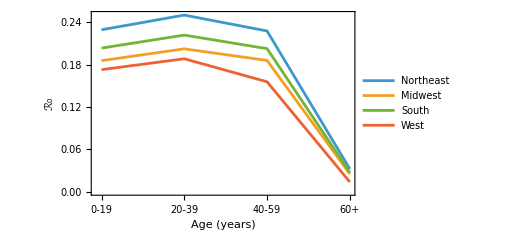

```mathematica
f11=ListPlot[Table[Tooltip[ l0[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","ℛ_0"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```

## Method by Ludmil and Yuliya

```mathematica
OptimalChi1={{3.004578161051320220*^-3,6.063747923999046954*^-3,3.545425576831823678*^-3,2.236626067229857952*^-14},
{4.398722516730560125*^-3,4.449697286182037123*^-3,5.958627241133407706*^-3,6.642807744610886198*^-11},
{3.537310173540902242*^-3,4.151002856664137187*^-3,3.181218010565318565*^-3,2.718994501058789159*^-14},
{6.054774009199111705*^-3,3.829806663471072622*^-3,4.735452868049963744*^-3,4.596756904901710390*^-11}};
```

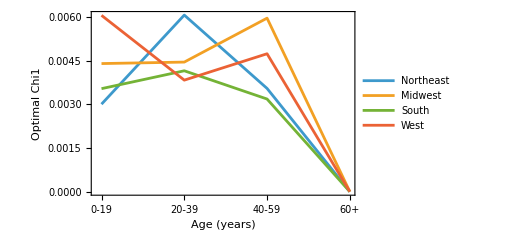

```mathematica
f11B=ListPlot[Table[Tooltip[ OptimalChi1[[i]],RN[[i]]],{i,1,m}],PlotMarkers->None,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Age (years)","Optimal Chi1"},FrameTicks->{{Automatic,Automatic},{dTcks,None}},PlotLegends->RN,LabelStyle->Directive[FontSize->12,FontFamily->"Arial"],ImageSize->375]
```

```mathematica
Export["nMatrix.csv",mN];
Export["aMatrix.csv",ma];
Export["cMatrix.csv",mc];
Export["betaVector.csv",vβ];
Export["chi1Matrix.csv",mχ1];
Export["chi2Matrix.csv",mχ2];
Export["chi3Matrix.csv",mχ3];
Export["pnMatrix.csv",pdfe];
Export["snMatrix.csv",sdfe];
Export["vnMatrix.csv",vdfe];
Export["yMatrix.csv",Y];
Export["zMatrix.csv",Z];
Export["ccmMatrix.csv",ccM];
Export["ccmatMatrix.csv",ccMat];
Export["qMatrix.csv",Q];
Export["NGM.csv",NGM];
Export["hMatrix.csv",mH];
```

```mathematica
Flatten[Y]/Flatten[Z]
```

{0.0325827,0.0685421,0.119821,0.0335186,0.0339157,0.0496775,0.0926775,0.0366004,0.0301887,0.0384574,0.163046,0.0389737,0.129413,0.0771499,0.0298042,0.0459906}

```mathematica
before={0.6612131221865993,0.25408187504948926,1.1421633448378747,1.5593869804504985,1.1087095860598926,0.39445049666870136,1.866229663545527,2.590611395524008,0.7807638547630817,0.23473150237994153,1.3775273378887491,1.9699090892980564,0.6136719197161066,0.19836178464681917,1.2654423844854101,1.9402417756048118}
```

{0.661213,0.254082,1.14216,1.55939,1.10871,0.39445,1.86623,2.59061,0.780764,0.234732,1.37753,1.96991,0.613672,0.198362,1.26544,1.94024}

```mathematica
Norm[Flatten[Y]/Flatten[Z]-before]
```

5.09069